```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
(* f[x_] := Sin[x] *)
f[x_]:=-Exp[-x^2];
(* constant diffusion *)
g=0.25;
```

```mathematica
nsamp=1;
dt = 0.01;
numsteps=400;
ns = numsteps;
mcsol=Table[0,ns+1];
mcsol[[1]]=0.1; (* initial condition *)
For[i=1,i≤ns,i+=1,
mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],nsamp]);
]
```

```mathematica
Flatten[mcsol][[1;;100]]
```

{0.1,0.0914986,0.0911109,0.0845948,0.0797486,0.0798472,0.0694868,0.0586497,0.0434944,0.0370065,0.0461696,0.0384695,0.0262354,1.17652,1.17449,1.2149,1.21346,1.21137,1.21036,1.2147,1.18022,1.18004,1.17709,1.17346,1.06739,1.06769,1.06617,1.06013,1.0448,1.03949,1.04117,1.03487,1.02586,1.02124,1.02033,1.01596,1.00997,1.00448,1.00016,0.979649,0.9778,0.971398,0.96885,0.940808,0.935096,0.93955,0.930233,0.922852,0.916426,0.913289,0.907958,0.901187,0.896464,0.889732,0.873234,0.874132,0.865973,0.862706,0.846348,0.847321,0.841023,0.835143,0.83205,0.828017,0.73204,0.727394,0.720624,0.712746,0.722497,0.716941,0.748425,0.729257,0.748827,0.744332,0.741429,0.747783,0.740167,0.734252,0.728199,0.723642,0.71764,0.714915,0.710679,0.705146,0.700172,0.691342,0.687609,0.676655,0.668532,0.668175,0.663982,0.674935,0.668953,0.661477,0.659385,0.658463,0.661754,0.660869,0.656172,0.67136}

```mathematica
tvec=Table[j*dt,{j,0,numsteps}];
```

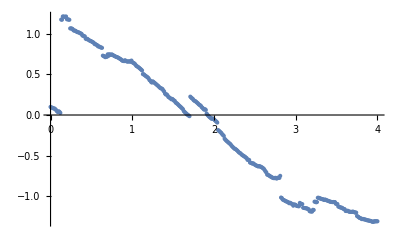

```mathematica
ListPlot[Transpose[{tvec,Flatten[mcsol]}]]
```

```mathematica
Export["mcsolgauss.csv",mcsol]
```

mcsolgauss.csv